## Interfacing with the Boost Graph Library

This example shows how to create a class that represents a graph, and run various algorithms on it using the Boost Graph Library.

```mathematica
Needs["LTemplate`"]
SetDirectory@NotebookDirectory[];
```

```mathematica
template=
LClass["BGraph",
{
LFun["set",
{Integer (* vertex count *),
{Integer,2,"Constant"} (* 0-based indexed edge list *)},
"Void"
],
LFun["vcount",{},Integer],
LFun["ecount",{},Integer],
LFun["edgeList",{},{Integer,2}],
LFun["isomorphicQ",
{LExpressionID["BGraph"] (* the other graph *)},
True|False
],
LFun["kuratowskiSubdivision",{},{Integer,1} (* edge indices *)]
}
];
```

To compile this example, it is necessary to indicate the location of the Boost headers. Adjust this according to your system.

```mathematica
CompileTemplate[template,
"IncludeDirectories"->{"/opt/local/include"} (* Boost location *)
]
```

Current directory is: /Users/szhorvat/Repos/LTemplate/LTemplate/Documentation/Examples/BGraph

Unloading library BGraph ...

Generating library code ...

Compiling library code ...

/Users/szhorvat/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64/BGraph.dylib

```mathematica
LoadTemplate[template]
```

#### Create graphs

Since LTemplate does not currently support passing arguments to constructors, the BGraph object is created in two steps:

Create an empty graph

Set edges and vertices

The following function handles all of this. We will use only this function to create BGraphs to ensure that they have been correctly initialized.

IndexGraph is not particularly fast, but we shall use it for the sake of simplicity. The set function expects zero-based indices, therefore we must subtract 1.

```mathematica
makeBGraph[g_?UndirectedGraphQ]:=
Block[{bg=Make[BGraph]},
bg@"set"[VertexCount[g],List@@@EdgeList@IndexGraph[g]-1];
bg
]
```

Let’s convert the following graph to a BGraph:

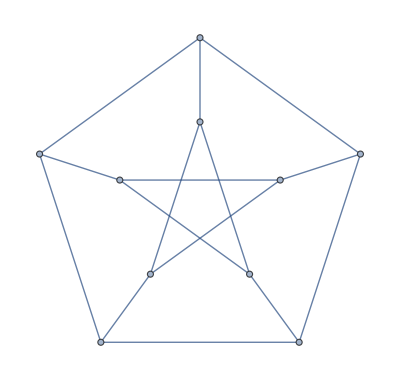

```mathematica
pg=PetersenGraph[]
```

```mathematica
bg=makeBGraph[pg]
```

BGraph[1]

#### Retrieve basic properties

How many vertices does it have?

```mathematica
bg@"vcount"[]
```

10

How many edges does it have?

```mathematica
bg@"ecount"[]
```

15

Retrieve the edge list.

```mathematica
bg@"edgeList"[]
```

{{0,2},{0,3},{0,5},{1,3},{1,4},{1,6},{2,4},{2,7},{3,8},{4,9},{5,6},{5,9},{6,7},{7,8},{8,9}}

Convert to a Mathematica Graph with vertices labelled from 1 (instead of 0).

```mathematica
fromBGraph[bg_BGraph]:=
Graph[Range[bg@"vcount"[]],1+bg@"edgeList"[],DirectedEdges->False]
```

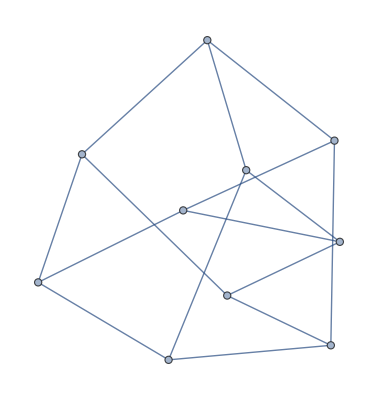

```mathematica
fromBGraph[bg]
```

Verify that it is indeed the same graph, with the same edge ordering:

```mathematica
EdgeList[fromBGraph[bg]]===EdgeList@IndexGraph[pg]
```

True

#### Run graph algorithms

Run the isomorphism algorithm.

```mathematica
bg2=makeBGraph[GraphData["PetersenGraph"]]
```

BGraph[2]

```mathematica
bg@"isomorphicQ"[ManagedLibraryExpressionID[bg2]]
```

True

Wrap the function for convenient isomorphism checking of Mathematica Graphs.

```mathematica
isomorphicQ[g1_?UndirectedGraphQ,g2_?UndirectedGraphQ]:=
Block[{bg1=makeBGraph[g1],bg2=makeBGraph[g2]},
bg1@"isomorphicQ"[ManagedLibraryExpressionID[bg2]]
]
```

```mathematica
isomorphicQ[Graph[{1<->2,2<->3}],Graph[{1<->3,2<->3}]]
```

True

Let us compute a Kuratowski subdivision of a non-planar graph.

```mathematica
kuratowskiSubdivision[g_?UndirectedGraphQ]:=
Block[{bg=makeBGraph[g]},
Part[EdgeList[g],1+bg@"kuratowskiSubdivision"[]]
]
```

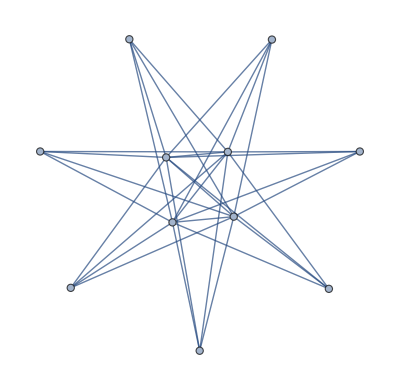

```mathematica
npg=GraphData[{"Cone",{4,7}}]
```

```mathematica
kuratowskiSubdivision[npg]
```

{1<->2,2<->5,2<->6,2<->7,3<->5,3<->6,3<->7,4<->5,4<->6,4<->7}

The function returns it as a list of edge indices, which we transform to an edge list in Mathematica. Let us visualize it.

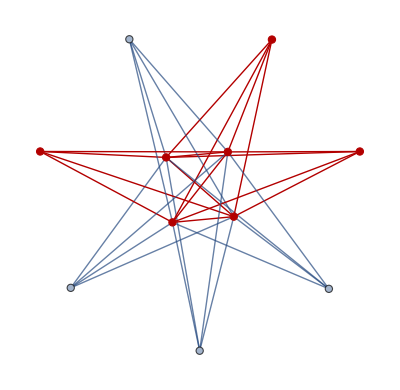

```mathematica
HighlightGraph[npg,Subgraph[npg,kuratowskiSubdivision[npg]]]
```

For planar graphs, the function returns the empty list.

```mathematica
kuratowskiSubdivision[CycleGraph[5]]
```

{}